# d=3 Minkowski

```mathematica
SetDirectory["~/Documents/Causal/"];(*Directory should be set to where the causet2.wl package is saved*)
<<"causet2.wl";(*importing the package causet2.wl which has things like the sprinkling and causal/link matrices defined in it*)
```

## Setup

```mathematica
m:=0
l:=1
n:=2000
d:=3
"causal events" n
A=CSMinkowski3Diamond[l,n];
ρ:=n/ CVolume[A]
"density" ρ
Subscript[C, 1]=CausalMatrix[A];
V=(IdentityMatrix[n]+Subscript[C, 1]).(IdentityMatrix[n]+Subscript[C, 1]);
```

2000 causal events

7639.44 density

## Link Matrix Propagator

```mathematica
L=LinkMatrix[A];
maxlength=SparseArray[Subscript[C, 1]]["NonzeroValues"];
positions=SparseArray[Subscript[C, 1]//Flatten]["NonzeroPositions"]//Flatten;
zeroCompare=Table[0,{i,1,n},{j,1,n}];
counter=1;
chains=L;

Do[
counter++;

chains=chains.L;(*finding chains of length i+1 composed of links*)

If[chains==zeroCompare,Break[]];(*if chains = 0, we can stop the loop, since no longer chains will be found*)

length=Flatten[chains][[positions]];(*flattening the matrix to a 1d array and finding only the entries corresponding to the positions of nonzero causal matrix entries*)

comparePositions=SparseArray[length//Flatten]["NonzeroPositions"]//Flatten;(*finding the positions in the new array that are nonzero*)

length=SparseArray[length]["NonzeroValues"];(*keeping only the nonzero entries of the new array*)

length=counter*HeavisideTheta[length];(*currently the length array has the number of link chains between two points, but we want the length of the chain*)
(*since the chains are longer in each iteration of the loop, we can replace the corresponding entries in the max length array with the updated values *)
maxlength[[comparePositions]]=length
(*looping up to NN-1 (i.e. L^(NN-1)), since the longest possible chain in a causet of size NN has NN-1 links*)
,{i,1,n-2}]

flattenedMaxLength=Table[0,{i,1,n*n}];(*NN^2 array of zeros*)

Do[flattenedMaxLength[[ positions[[i]] ]]=maxlength[[i]],{i,1,Length[positions]}];(*replace entries with max chain lengths according to the position of nonzero causal matrix entries in flattened causal matrix*)

MaxLength=Table[flattenedMaxLength[[1+(i-1)*n;;n+(i-1)*n]],{i,1,n}];(*unflatten to a square NN x NN matrix*)
m3=2.195/1.1737024367422795;
a=((ρ π)/12)^(1/3)m3/(2π);
K = Table[If[Subscript[C, 1][[i,j]]==1,a/MaxLength[[i,j]],0],{i,n},{j,n}];
```

105790 causal relations

## Regular propagator

```mathematica
VolTime=(12/(π ρ))^(1/3)*(V)^(1/3)*Subscript[C, 1];  
K0=Table[If[Subscript[C, 1][[i,j]]==1,1/(2π)Cos[m*VolTime[[i,j]]]/VolTime[[i,j]],0],{i,n},{j,n}];

Z=Table[Sqrt[(A[[1,i,1]]-A[[1,j,1]])^2+(A[[1,i,2]]-A[[1,j,2]])^2-(A[[1,i,3]]-A[[1,j,3]])^2],{i,n},{j,n}];
MfdTime=Chop[Subscript[C, 1]*Im[Z]];

points=Transpose[{Flatten[MfdTime],Flatten[K0]}];
points=DeleteCases[Chop[points],{0,_}];
Length[points]"causal relations"
(*
VolPoints=Transpose[{Flatten[MfdTime],Flatten[K0]}];
VolPoints=DeleteCases[Chop[VolPoints],{0,_}];
Length[VolPoints]"causal relations"
*)
(*Remove[maxlength,positions,Z,MfdTime,K,flattenedMaxLength,length,chains,zeroCompare]*)
```

452833 causal relations

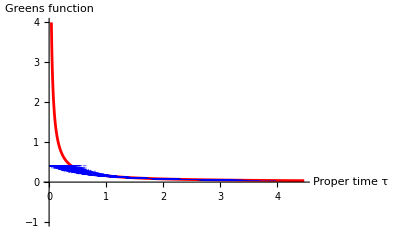

```mathematica
sample:=100000
PointsSample=RandomSample[points,sample];
(*plot1=ListPlot[RandomSample[points,sample],PlotLegends->Placed[{"Proper time from length of longest path"},{0.80,.65}],PlotStyle->PointSize[0.00001]];*)

plot3=ListPlot[PointsSample,PlotLegends->Placed[{"Proper time from volume"},{0.77,.55}],PlotStyle->{PointSize[0.00001],Blue}];

plot2=Plot[{1/(2 π) Cos[m x]/x},{x,0,l},PlotLegends->Placed[{"Analyitic Curve"},{0.75,.75}],PlotStyle->{Red},PlotRange->{{0,l},{-1,4}}];

Show[plot2,plot3,AxesLabel->{"Proper time τ","Greens function"}]
```

## Whitman function for Causet :

```mathematica
iΔ=N[I*(K0-Transpose[K0])];
{EE,VV}=Chop[Eigensystem[iΔ]];
Q = Transpose[VV] . DiagonalMatrix[Clip[N[EE],{0, Max[N[Abs[EE]]]}]] . Conjugate[VV] // Chop;

pointsTime=Transpose[{Flatten[MfdTime],Flatten[Re[Q]]}];
pointsTime=DeleteCases[Chop[pointsTime],{0,_}];
Length[pointsTime]"No. of non-zero relations"
(*pointsSpace=Transpose[{Flatten[MfdSpace],Flatten[Re[Q]]}];*)
```

452833 No. of non-zero relations

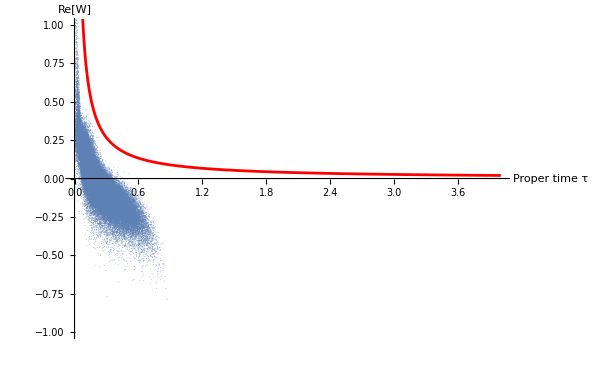

```mathematica
sample:=100000
plotLength := 4
PlottingPoints=RandomSample[pointsTime,sample];
Show[ListPlot[PlottingPoints,PlotStyle->PointSize[0.00001],ImageSize->600],Plot[Im[I/(4π)Exp[-I*m*τ]/τ],{τ,0,plotLength},PlotStyle->Red,PlotRange->{{0,plotLength},{-2,2}}],AxesOrigin->{0,0},PlotRange->{{0,plotLength},{-1,1}},AxesLabel->{"Proper time τ","Re[W]"}]
```